```mathematica
λ=0.2573;v=0.3
```

0.3

```mathematica
A[z_]:=(1/2) Log[2.94 Sin[1.24 Sin[0.47 z+1.94]-9.55]+3.53]
```

```mathematica
T1[zh_]:=1/(π zh)
```

```mathematica
AS[z_]:=(1/2) Log[2.94 Sin[1.24 Sin[0.47 z+1.94]-9.55]+3.53]
```

```mathematica
g1[z_,zh_]:=1-(1/zh^4) z^4
```

```mathematica
T2[zh_]:=1/(π zh)
```

```mathematica
T4=0.17*2.5
```

0.425

```mathematica
6
```

6

```mathematica
FindRoot[T2[zh0]==0.15300000000000002,{zh0,1}]
```

{2.08046→2.08046}

```mathematica
zh0=2.080456772443076
```

2.08046

```mathematica
FindRoot[g1[zs0,zh0]==0.09,{zs0,1}]
```

{2.15898→2.03198}

```mathematica
zs0=2.031978201138439
```

2.03198

```mathematica
T3=T2[zh0]/0.139639
```

0.75

```mathematica
FindRoot[T2[zh1]==0.17,{zh1,1}]
```

{1.87241→1.87241}

```mathematica
zh1=1.8724110951987687
```

1.87241

```mathematica
FindRoot[g1[zs1,zh1]==0.09,{zs1,1}]
```

{1.94308→1.82878}

```mathematica
zs1=1.8287803810245953
```

1.82878

```mathematica
T3=T2[zh1]/0.189
```

1.

```mathematica
FindRoot[T2[zh2]==0.20400000000000001,{zh2,1}]
```

{1.56034→1.56034}

```mathematica
zh2=1.5603425793323071
```

1.56034

```mathematica
FindRoot[g1[zs2,zh2]==0.09,{zs2,1}]
```

{1.61923→1.52398}

```mathematica
zs2=1.5239836508538291
```

1.52398

```mathematica
FindRoot[T2[zh3]==0.238,{zh3,1}]
```

{1.33744→1.33744}

```mathematica
zh3=1.3374364965705492
```

1.33744

```mathematica
FindRoot[g1[zs3,zh3]==0.09,{zs3,1}]
```

{1.38791→1.30627}

```mathematica
zs3=1.3062717007318538
```

1.30627

```mathematica
|
```

```mathematica
FindRoot[T2[zh7]==0.37400000000000005,{zh7,1}]
```

{0.904289→0.851096}

```mathematica
zh7=0.8510959523630764
```

0.851096

```mathematica
FindRoot[g1[zs7,zh7]==0.09,{zs7,1}]
```

{0.883218→0.831264}

```mathematica
zs7=0.8312638095566339
```

0.831264

```mathematica
FindRoot[T2[zh10]==0.44200000000000006,{zh10,1}]
```

{0.765168→0.720158}

```mathematica
zh10=0.7201581135379879
```

0.720158

```mathematica
FindRoot[g1[zs10,zh10]==0.09,{zs10,1}]
```

{0.747338→0.703377}

```mathematica
zs10=0.7033770696248441
```

0.703377

```mathematica
FindRoot[T2[zh11]==0.28900000000000003,{zh11,1}]
```

{zh11→1.10142}

```mathematica
zh11=1.1014182912933934
```

1.10142

```mathematica
FindRoot[g1[zs11,zh11]==0.09,{zs11,1}]
```

{zs11→1.07575}

```mathematica
zs11=1.075753165308586
```

1.07575

```mathematica
FindRoot[T2[zh12]==0.323,{zh12,1}]
```

{zh12→0.98548}

```mathematica
zh12=0.9854795237888233
```

0.98548

```mathematica
FindRoot[g1[zs12,zh12]==0.09,{zs12,1}]
```

{zs12→0.962516}

```mathematica
zs12=0.9625159900129426
```

0.962516

```mathematica
FindRoot[T2[zh13]==0.35700000000000004,{zh13,1}]
```

{zh13→0.891624}

```mathematica
zh13=0.8916243310470306
```

0.891624

```mathematica
FindRoot[g1[zs13,zh13]==0.09,{zs13,1}]
```

{zs13→0.870848}

```mathematica
zs13=0.8708478004879004
```

0.870848

```mathematica
FindRoot[T2[zh14]==0.391,{zh14,1}]
```

{zh14→0.814092}

```mathematica
zh14=0.8140917805212038
```

0.814092

```mathematica
FindRoot[g1[zs14,zh14]==0.09,{zs14,1}]
```

{zs14→0.795122}

```mathematica
zs14=0.7951219047933024
```

0.795122

```mathematica
FindRoot[T2[zh15]==0.42500000000000004,{zh15,1}]
```

{zh15→0.748964}

```mathematica
zh15=0.7489644380795069
```

0.748964

```mathematica
FindRoot[g1[zs15,zh15]==0.09,{zs15,1}]
```

{zs15→0.731512}

```mathematica
zs15=0.7315121524098375
```

0.731512

1.101418291293393

```mathematica
D2[zs_,zh_]:=(4*π^2*T2[zh]^2*zs^2)/(λ*Exp[2*AS[zs]]*√(1-v^2))
```

```mathematica
d0=D2[zs0,zh0]
```

5.16292

```mathematica
d1=D2[zs1,zh1]
```

5.78505

```mathematica
d2=D2[zs2,zh2]
```

6.93196

```mathematica
d3=D2[zs3,zh3]
```

7.92057

```mathematica
d7=D2[zs7,zh7]
```

8.70668

```mathematica
d10=D2[zs10,zh10]
```

11.3167

```mathematica
d11=D2[zs11,zh11]
```

9.11916

```mathematica
d12=D2[zs12,zh12]
```

9.75915

```mathematica
d13=D2[zs13,zh13]
```

10.2977

```mathematica
d14=D2[zs14,zh14]
```

10.7539

```mathematica
d15=D2[zs15,zh15]
```

11.1432

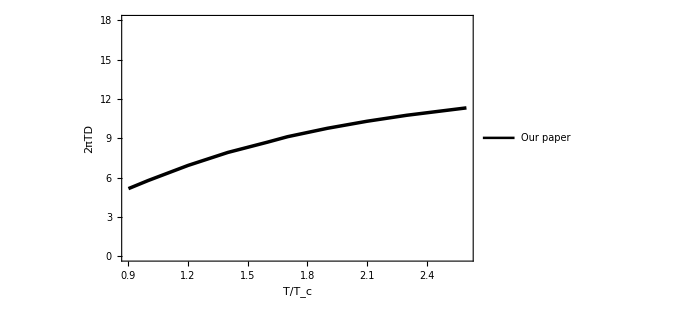

```mathematica
f1=ListLinePlot[{{0.9,5.162923184683022},{1,5.785045309749159},{1.2,6.931961440341872},{1.4,7.92057246835887},{1.6,8.70667635441106},{1.7,9.119157589078196},{1.9,9.75915177530323},{2.1,10.297739500000628},{2.3,10.753910758313273},{2.5,11.143181648519793},{2.6,11.316711060925234}},Frame->True,PlotStyle->{{Black,Thickness[0.005]}},BaseStyle->{FontFamily->"Times New Roman",FontSize->16},PlotRange->{{0.9,2.6},{0,18}},PlotLegends->Placed[LineLegend[{"Our paper"},LabelStyle->{FontSize->15}],{0.2,0.9}],FrameLabel->{Style["T/\!\(\*SubscriptBox[\(T\), \(c\)]\)",15,Black,Italic,FontFamily->"Times New Roman"],Style["2πTD",15,Black,Italic,FontFamily->"Times New Roman"]},FrameStyle->Directive[FontFamily->"Times New Roman",FontSize->16],ImageSize->{500,300}]
```